Веркович Е.В., 221703
Лабораторная работа № 3 
Интерполяция и среднеквадратичное приближение
Вариант 1

Задание 1
Создать таблицу значений функции
f(x), разбив отрезок [0, 6] на n равных частей точками x_i(i=0,n)
 Для полученной таблично заданной в
равноотстоящих узлах функции f(x), выполнить следующие действия при n=6 и n=10.

```mathematica
f[x_]:=5*Exp[-1/18*x^2+1/3*x-1/2]-2*Sin[√x]
a=0(*начало отрезка*)
b=6(*конец отрезка*)
n=6(*количество разбиений*)
data = N[Table[{x,f[x]},{x,a,b,(b-a)/n}]](*таблица значений функции f(x), на отрезке[0,6] разбитом на n частей*)
```

0

6

6

{{0.,3.03265},{1.,2.32075},{2.,2.75427},{3.,3.02595},{4.,2.9112},{5.,2.43019},{6.,1.75634}}

a) Построить интерполяционный многочлен Лагранжа

```mathematica
lagrangeInterpolation[data_,x_]:=Module[{n=Length[data],polynomials={}},Do[Module[{polynomial=1},Do[If[i!=j,polynomial*=(x-data[[j,1]])/(data[[i,1]]-data[[j,1]])],{j,1,n}];
AppendTo[polynomials,polynomial]],{i,1,n}];
Total[polynomials*data[[All,2]]]]
```

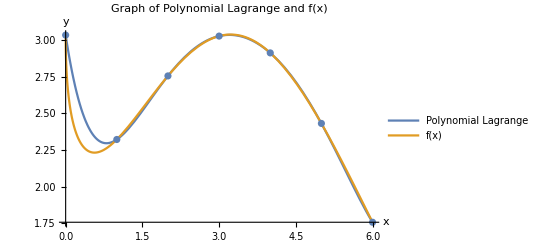

```mathematica
Show[Plot[{lagrangeInterpolation[data,x],f[x]},{x,0,n},PlotLegends->{"Polynomial Lagrange","f(x)"},AxesLabel->{"x","y"},PlotLabel->"Graph of Polynomial Lagrange and f(x)"],ListPlot[data]]
```

б) Создать таблицу разделенных разностей функции f (x) по точкам

```mathematica
dividedDifferences[f_,data_List]:=Module[{n,dividedDiffs},n=Length[data];
dividedDiffs=ConstantArray[0,{n,n}];
dividedDiffs[[All,1]]=f/@data[[All,1]];
Do[dividedDiffs[[i,j]]=(dividedDiffs[[i,j-1]]-dividedDiffs[[i-1,j-1]])/(data[[i,1]]-data[[i-j+1,1]]),{j,2,n},{i,j,n}];
dividedDiffs]
```

```mathematica
TableForm[dividedDifferences[f,data]]
```

3.03265 | 0 | 0 | 0 | 0 | 0 | 0
2.32075 | -0.711908 | 0 | 0 | 0 | 0 | 0
2.75427 | 0.43352 | 0.572714 | 0 | 0 | 0 | 0
3.02595 | 0.271681 | -0.0809196 | -0.217878 | 0 | 0 | 0
2.9112 | -0.114744 | -0.193213 | -0.0374311 | 0.0451117 | 0 | 0
2.43019 | -0.481014 | -0.183135 | 0.00335933 | 0.0101976 | -0.00698283 | 0
1.75634 | -0.673851 | -0.0964185 | 0.0289054 | 0.00638652 | -0.000762214 | 0.00103677

в) построить первый или второй интерполяционный многочлен
Ньютона

```mathematica
newtonPolynomial[f_,data_List]:=Module[{dividedDiffs,polynomial},dividedDiffs=dividedDifferences[f,data];
polynomial=dividedDiffs[[1,1]];
Do[polynomial+=dividedDiffs[[i,i]]*Product[(x-data[[j,1]]),{j,1,i-1}],{i,2,Length[data]}];
polynomial]
Table[newtonPolynomial[f,data],{x,0,n}]
```

{3.03265,2.32075,2.75427,3.02595,2.9112,2.43019,1.75634}

г) построить интерполяционный многочлен Ньютона с помощью функции InterpolatingPolynomial

```mathematica
Table[InterpolatingPolynomial[data,x],{x,0,n}]
```

{3.03265,2.32075,2.75427,3.02595,2.9112,2.43019,1.75634}

д) вычислить значения функции f (x) и всех построенных интерполяционных многочленов в точке x = 2, 4316

```mathematica
xPoint=2.4316
```

2.4316

```mathematica
f[xPoint]
newtonPolynomial[f,data]/. x->xPoint
lagrangeInterpolation[data,xPoint]
InterpolatingPolynomial[data,xPoint]
```

2.91119

2.91645

2.91645

2.91645

е) построить график погрешности интерполирования многочленом Ньютона на отрезке[0, 6]

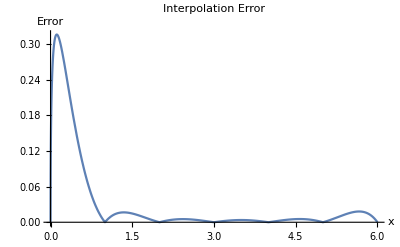

```mathematica
Np=InterpolatingPolynomial[data,x];
Rn[x_]:=Abs[f[x]-Np]
Plot[Rn[x],{x,0,6},PlotRange->All,AxesLabel->{"x","Error"},PlotLabel->"Interpolation Error"]
```

```mathematica
FindMaximum[Rn[x],{x,0,6}]
```

{0.316287,{x→0.114284}}

Задание 1, n=10
a)

```mathematica
n=10(*количество разбиений*)
data = N[Table[{x,f[x]},{x,a,b,(b-a)/n}]](*таблица значений функции f(x), на отрезке[0,6] разбитом на n частей*)
```

10

{{0.,3.03265},{0.6,2.23189},{1.2,2.39809},{1.8,2.66786},{2.4,2.90146},{3.,3.02595},{3.6,3.0067},{4.2,2.84029},{4.8,2.5487},{5.4,2.17146},{6.,1.75634}}

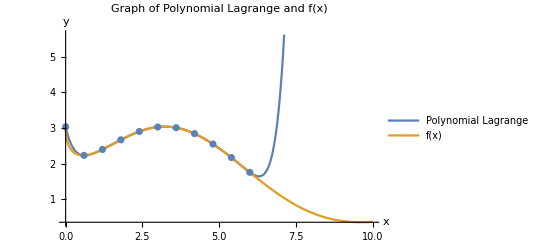

```mathematica
Show[Plot[{lagrangeInterpolation[data,x],f[x]},{x,0,n},PlotLegends->{"Polynomial Lagrange","f(x)"},AxesLabel->{"x","y"},PlotLabel->"Graph of Polynomial Lagrange and f(x)"],ListPlot[data]]
```

б)

```mathematica
TableForm[dividedDifferences[f,data]]
```

3.03265 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.23189 | -1.33461 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.39809 | 0.276996 | 1.343 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.66786 | 0.449629 | 0.143861 | -0.666189 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.90146 | 0.389326 | -0.050253 | -0.107841 | 0.232645 | 0 | 0 | 0 | 0 | 0 | 0
3.02595 | 0.207478 | -0.15154 | -0.0562705 | 0.0214878 | -0.0703857 | 0 | 0 | 0 | 0 | 0
3.0067 | -0.0320828 | -0.199634 | -0.0267188 | 0.0123132 | -0.00305821 | 0.0187021 | 0 | 0 | 0 | 0
2.84029 | -0.277337 | -0.204378 | -0.00263588 | 0.0100345 | -0.000759553 | 0.000638515 | -0.00430085 | 0 | 0 | 0
2.5487 | -0.485986 | -0.173874 | 0.0169466 | 0.00815938 | -0.000625055 | 0.0000373606 | -0.000143132 | 0.000866191 | 0 | 0
2.17146 | -0.628747 | -0.118967 | 0.030504 | 0.00564891 | -0.000836825 | -0.0000588249 | -0.0000229013 | 0.000025048 | -0.000155767 | 0
1.75634 | -0.691862 | -0.052596 | 0.0368729 | 0.00265368 | -0.000998409 | -0.0000448845 | 3.31916×10^-6 | 5.4626×10^-6 | -3.62693×10^-6 | 0.0000253567

в)

```mathematica
Table[newtonPolynomial[f,data],{x,0,n}]
```

{3.03265,2.3179,2.75398,3.02595,2.91135,2.43081,1.75634,4.06679,61.266,549.308,3207.81}

г)

```mathematica
Table[InterpolatingPolynomial[data,x],{x,0,n}]
```

{3.03265,2.3179,2.75398,3.02595,2.91135,2.43081,1.75634,4.06679,61.266,549.308,3207.81}

д)

```mathematica
f[xPoint]
newtonPolynomial[f,data]/. x->xPoint
lagrangeInterpolation[data,xPoint]
InterpolatingPolynomial[data,xPoint]
```

2.91119

2.91122

2.91122

2.91122

е)

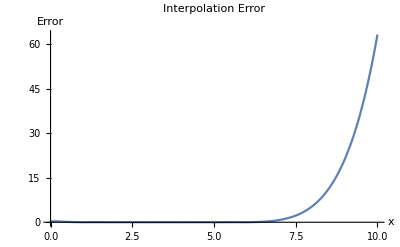

```mathematica
Plot[Rn[x],{x,0,n},PlotRange->All,AxesLabel->{"x","Error"},PlotLabel->"Interpolation Error"]
```

```mathematica
FindMaximum[Rn[x],{x,0,n}]
```

{0.316287,{x→0.114282}}

ж) исследовать зависимость погрешности интерполирования от количества узлов интерполирования

```mathematica
table1=Table[{x,Rn[x]},{x,0,10}](*10 узлов*)
```

{{0,0.},{1,0.},{2,2.22045×10^-16},{3,0.},{4,4.44089×10^-16},{5,6.66134×10^-16},{6,0.},{7,0.767349},{8,5.33614},{9,21.1973},{10,63.1776}}

```mathematica
data2=N[Table[{x,f[x]},{x,a,b,(b-a)/6}]](*6 узлов*)
```

{{0.,3.03265},{1.,2.32075},{2.,2.75427},{3.,3.02595},{4.,2.9112},{5.,2.43019},{6.,1.75634}}

```mathematica
Rn2[x_]:=Abs[f[x]-InterpolatingPolynomial[data2,x]]
```

```mathematica
table2=Table[{x,Rn2[x]},{x,0,6}]
```

{{0,0.},{1,0.},{2,2.22045×10^-16},{3,0.},{4,4.44089×10^-16},{5,6.66134×10^-16},{6,0.}}

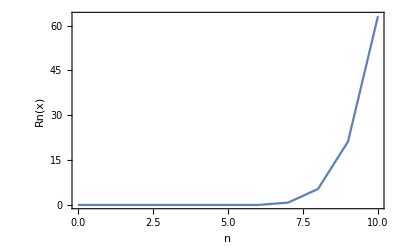

```mathematica
ListPlot[table1,Joined->True,Frame->True,FrameLabel->{"n","Rn(x)"}](*график зависимости значений погрешности от количества узлов(10)*)
```

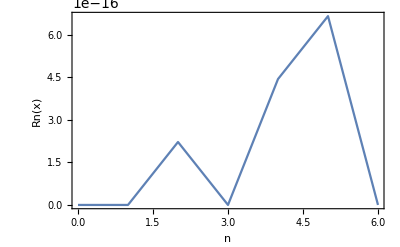

```mathematica
ListPlot[table2,Joined->True,Frame->True,FrameLabel->{"n","Rn(x)"}](*график зависимости значений погрешности от количества узлов(6)*)
```

Задание 2

```mathematica
n=6
```

```mathematica
6
dataXi=List[]
```

6

{}

```mathematica
For[i=0,i<=n,i++,
Ti=Cos[(Pi*(2*i+1))/(2*n+2)];
Xi=(a+b)/2+(b-a)/2*Ti;
AppendTo[dataXi,Xi];
]
```

```mathematica
dataXi=N[dataXi]
```

{5.92478,5.34549,4.30165,3.,1.69835,0.654506,0.0752163}

```mathematica
data = N[  Table[ {dataXi[[i]],f[dataXi[[i]]]} ,{i,1,n} ] ]
```

{{5.92478,1.80879},{5.34549,2.20803},{4.30165,2.79879},{3.,3.02595},{1.69835,2.62201},{0.654506,2.23608}}

a) Создать таблицу разделенных разностей функции f (x) по точкам

```mathematica
TableForm[dividedDifferences[f,data]]
```

1.80879 | 0 | 0 | 0 | 0 | 0
2.20803 | -0.689177 | 0 | 0 | 0 | 0
2.79879 | -0.565951 | -0.0759186 | 0 | 0 | 0
3.02595 | -0.174514 | -0.166889 | 0.0311032 | 0 | 0
2.62201 | 0.310326 | -0.18624 | 0.005306 | 0.00610376 | 0
2.23608 | 0.369722 | -0.0253236 | -0.0441213 | 0.0105366 | -0.000841109

б) Построить интерполяционный монгочлен Ньютона

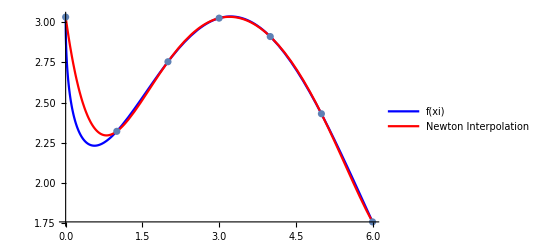

```mathematica
xi=data[[All,1]];
yi=data[[All,2]];

gr1=Plot[f[x],{x,0,n},PlotStyle->Blue,PlotLegends->{"f(xi)"}]
gr2=Plot[newtonPolynomial[f,data],{x,0,n},PlotStyle->Red,PlotLegends->{"Newton Interpolation"}]
gr3=ListPlot[data]
Show[gr1,gr2,gr3]
```

в) построить интерполирующую функцию с помощью Interpolation

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

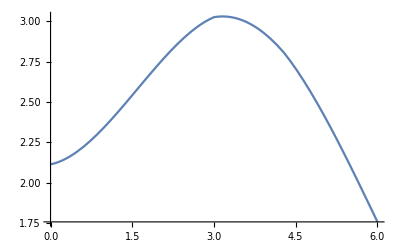

```mathematica
Plot[Interpolation[data,x],{x,0,n}]
```

г) вычислить значение х = 2.4316 в функциях

```mathematica
f[xPoint]
newtonPolynomial[f,data]/. x->xPoint
Interpolation[data,xPoint]
```

0.894988

0.89191

2.89279

```mathematica
FindMaximum[newtonPolynomial[f,data],{x,0,n}]
FindMaximum[Interpolation[data,x],{x,0,n}]
```

{1.16224,{x→1.66607}}

{3.03063,{x→3.15926}}

```mathematica
n=10
```

10

a)

```mathematica
dataXi=List[]
For[i=0,i<=n,i++,
Ti=Cos[(Pi*(2*i+1))/(2*n+2)];
Xi=(a+b)/2+(b-a)/2*Ti;
AppendTo[dataXi,Xi];
]
dataXi=N[dataXi]
```

{}

{5.96946,5.7289,5.26725,4.62192,3.8452,3.,2.1548,1.37808,0.732751,0.271104,0.0305357}

```mathematica
data = N[  Table[ {dataXi[[i]],f[dataXi[[i]]]} ,{i,1,n} ] ]
```

{{5.96946,0.288346},{5.7289,0.0465504},{5.26725,-0.323249},{4.62192,-0.533718},{3.8452,-0.262451},{3.,0.44112},{2.1548,1.04974},{1.37808,1.11929},{0.732751,0.742192},{0.271104,0.294906}}

```mathematica
TableForm[dividedDifferences[f,data]]
```

0.288346 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0465504 | 1.0051 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.323249 | 0.801044 | 0.290592 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.533718 | 0.326144 | 0.429008 | -0.102718 | 0 | 0 | 0 | 0 | 0 | 0
-0.262451 | -0.349245 | 0.47494 | -0.0243838 | -0.0368757 | 0 | 0 | 0 | 0 | 0
0.44112 | -0.832434 | 0.297911 | 0.078081 | -0.0375481 | 0.000226434 | 0 | 0 | 0 | 0
1.04974 | -0.720093 | -0.0664583 | 0.14769 | -0.0223648 | -0.00424815 | 0.001173 | 0 | 0 | 0
1.11929 | -0.0895479 | -0.388764 | 0.13064 | 0.00525602 | -0.00710197 | 0.000655928 | 0.000112617 | 0 | 0
0.742192 | 0.584359 | -0.473898 | 0.0375496 | 0.0299092 | -0.00633893 | -0.000168274 | 0.000164968 | -9.99685×10^-6 | 0
0.294906 | 0.968893 | -0.347374 | -0.0671681 | 0.0383737 | -0.00236828 | -0.000912623 | 0.000148985 | 2.9285×10^-6 | -2.26826×10^-6

б) Построить интерполяционный монгочлен Ньютона

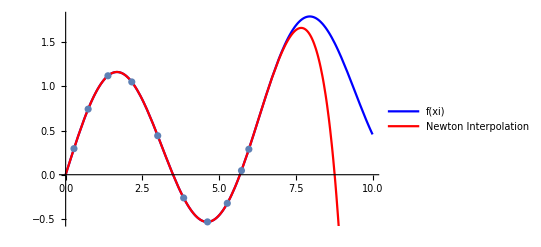

```mathematica
xi=data[[All,1]];
yi=data[[All,2]];

gr1=Plot[f[x],{x,0,n},PlotStyle->Blue,PlotLegends->{"f(xi)"}]
gr2=Plot[newtonPolynomial[f,data],{x,0,n},PlotStyle->Red,PlotLegends->{"Newton Interpolation"}]
gr3=ListPlot[data]
Show[gr1,gr2,gr3]
```

в) построить интерполирующую функцию с помощью Interpolation

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

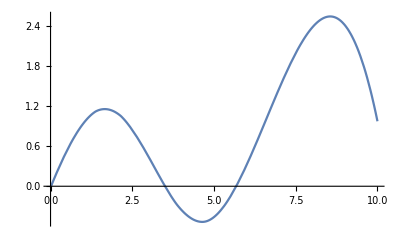

```mathematica
Plot[Interpolation[data,x],{x,0,n}]
```

г) вычислить значение х = 2.4316 в функциях

```mathematica
f[xPoint]
newtonPolynomial[f,data]/. x->xPoint
Interpolation[data,xPoint]
```

0.894988

0.894987

0.889932

д)

```mathematica
FindMaximum[newtonPolynomial[f,data],{x,0,n}]
FindMaximum[Interpolation[data,x],{x,0,n}]
```

{1.16208,{x→1.67097}}

{1.1553,{x→1.65853}}

Задание 3
Вывод: по результатам работы видно, что увеличение количества узлов позволяет уменьшить погрешность интерполирования на отрезке(при некотором оптимальном количестве), а также  этому способствует неравномерное размещение узлов(при определённых расположениях)

Задание 4

a) построить интерполяционный кубический сплайн дефекта 1

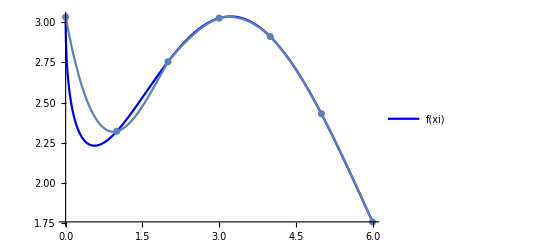

```mathematica
spl=Interpolation[data,InterpolationOrder->3,Method->"Hermite"];

gr2=Plot[spl[x],{x,Min[data[[All,1]]],Max[data[[All,1]]]},Epilog->{Directive[AbsolutePointSize[0],ColorData[97,4]],Point[data]}]
gr1=Plot[f[x],{x,0,n},PlotStyle->Blue,PlotLegends->{"f(xi)"}]
gr3=ListPlot[data]
Show[gr1,gr2,gr3]
```

б) выполнить интерполяцию сплайном .

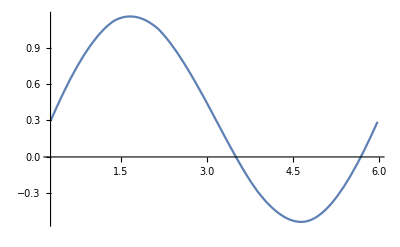

```mathematica
sf=Interpolation[data,Method->“Spline”];
Plot[sf[x],{x,Min[data[[All,1]]],Max[data[[All,1]]]},Epilog->{Directive[AbsolutePointSize[0],ColorData[97,4]],Point[data]}]
```

г)

```mathematica
f[xPoint]
spl[xPoint]
sf[xPoint]
```

0.894988

0.889932

0.889932

Задание 5

a)

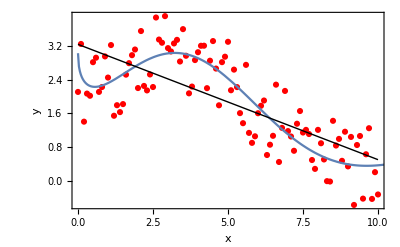

```mathematica
xData=Range[0,10,0.1];
yData=f[#]+RandomReal[{-1,1}]&/@xData;

(*Вычисляем суммы*)
n=Length[xData];
sumX=Total[xData];
sumY=Total[yData];
sumXY=Total[xData*yData];
sumX2=Total[xData^2];

(*Вычисляем коэффициенты a и b*)
a=(n*sumXY-sumX*sumY)/(n*sumX2-sumX^2);
b=(sumY-a*sumX)/n;

x=Range[0,10,0.1];
q1=a*x+b;

(*Строим график*)
Show[ListPlot[Transpose[{xData,yData}],PlotStyle->Red,PlotMarkers->Automatic,PlotRange->All,Frame->True,FrameLabel->{"x","y"},Epilog->{Line[Transpose[{x,q1}]]}],
Plot[f[x],{x,0,n}]
]
```

б)аппроксимировать с помощью метода наименьших квадратов функцию f(x) многочленом второй степени

{2.28795,0.312622,-0.0576946}

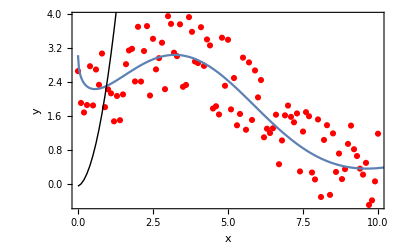

```mathematica
(*Вычисляем суммы*)n=Length[xData];
sumX=Total[xData];
sumY=Total[yData];
sumXY=Total[xData*yData];
sumX2=Total[xData^2];
sumX3=Total[xData^3];
sumX4=Total[xData^4];

(*Вычисляем коэффициенты a,b и c*)
X={{n,sumX,sumX2},{sumX,sumX2,sumX3},{sumX2,sumX3,sumX4}};
Y={sumY,sumXY,Total[xData^2*yData]};
P=LinearSolve[X,Y]

(*Получаем вектор P*)
(*Результат:{c,b,a}*)

(*Построение аппроксимирующего многочлена*)
q2[x_]:=P[[1]]*x^2+P[[2]]*x+P[[3]]

(*Строим график*)
x=Range[0,10,0.1];
y=q2[x];

Show[ListPlot[Transpose[{xData,yData}],PlotStyle->Red,PlotMarkers->Automatic,PlotRange->All,Frame->True,FrameLabel->{"x","y"},Epilog->{Line[Transpose[{x,y}]]}],Plot[f[x],{x,0,n}]]
```

в) найти многочлены наилучшего среднеквадратичного приближения
третьей и четвертой степеней с помощью функции Fit wolfram mathematica

```mathematica
(*Многочлен наилучшего среднеквадратичного приближения третьей степени*)
fitPoly3=Fit[data,{1,x,x^2,x^3},x]

(*Многочлен наилучшего среднеквадратичного приближения четвертой степени*)
fitPoly4=Fit[data,{1,x,x^2,x^3,x^4},x]
```

2.92471-0.612148 x+0.324302 x^2-0.0428527 x^3

3.02078-1.55683 x+1.15424 x^2-0.267016 x^3+0.0186802 x^4

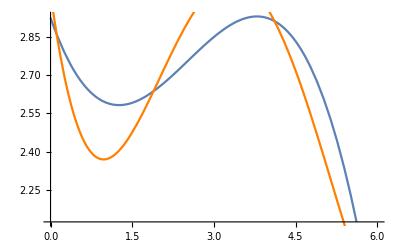

```mathematica
Show[Plot[fitPoly3,{x,0,b}],
Plot[fitPoly4,{x,0,b},PlotStyle->Orange]]
```

г)

```mathematica
f[xPoint]
q1=a*xPoint+b
q2[xPoint]
fitPoly3Value=fitPoly3/. x->xValue
fitPoly4Value=fitPoly4/. x->xValue
```

2.91119

2.5745

14.2304

{2.92471,2.8667,2.81491,2.7691,2.729,2.69436,2.66491,2.64042,2.62061,2.60522,2.59401,2.58672,2.58308,2.58284,2.58575,2.59154,2.59996,2.61076,2.62367,2.63843,2.6548,2.67251,2.69131,2.71094,2.73114,2.75166,2.77223,2.79261,2.81252,2.83173,2.84996,2.86697,2.8825,2.89628,2.90806,2.91759,2.9246,2.92884,2.93006,2.92799,2.92238,2.91297,2.89951,2.88173,2.85939,2.83221,2.79996,2.76236,2.71916,2.67011,2.61494,2.55341,2.48524,2.4102,2.32801,2.23842,2.14118,2.03603,1.92271,1.80096,1.67052,1.53115,1.38258,1.22455,1.05681,0.879102,0.691166,0.492747,0.283587,0.0634288,-0.167984,-0.410909,-0.665603,-0.932323,-1.21133,-1.50287,-1.80721,-2.12461,-2.45532,-2.7996,-3.1577,-3.52989,-3.91641,-4.31754,-4.73352,-5.16461,-5.61107,-6.07316,-6.55112,-7.04523,-7.55574,-8.0829,-8.62697,-9.18821,-9.76688,-10.3632,-10.9775,-11.61,-12.2609,-12.9306,-13.6192}

{3.02078,2.87637,2.75348,2.65055,2.56611,2.49871,2.44695,2.40947,2.38497,2.37216,2.36985,2.37684,2.39202,2.41428,2.44259,2.47596,2.51342,2.55408,2.59707,2.64158,2.68683,2.73208,2.77667,2.81996,2.86133,2.90026,2.93624,2.9688,2.99754,3.02208,3.0421,3.05733,3.06751,3.07248,3.07207,3.06619,3.05479,3.03786,3.01542,2.98756,2.95441,2.91612,2.87292,2.82506,2.77285,2.71663,2.6568,2.59379,2.5281,2.46023,2.39078,2.32035,2.2496,2.17925,2.11005,2.04278,1.9783,1.91749,1.86127,1.81064,1.76659,1.73021,1.70261,1.68492,1.67837,1.68419,1.70367,1.73814,1.78899,1.85764,1.94555,2.05425,2.18529,2.34027,2.52085,2.72871,2.96559,3.23328,3.5336,3.86843,4.23968,4.64931,5.09934,5.59182,6.12883,6.71253,7.34509,8.02875,8.76579,9.55853,10.4093,11.3206,12.2948,13.3344,14.442,15.6202,16.8715,18.1987,19.6046,21.0918,22.6632}

д)

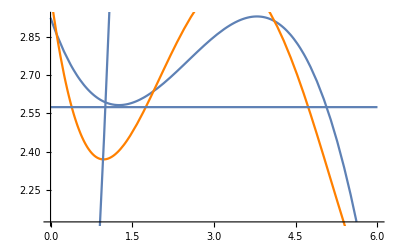

```mathematica
Show[Plot[fitPoly3,{x,0,6}],
Plot[fitPoly4,{x,0,6},PlotStyle->Orange],
Plot[q1,{x,0,6}],
Plot[q2[x],{x,0,6}]
]
```